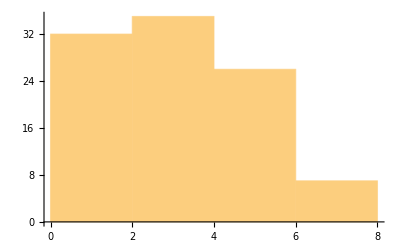

```mathematica
𝒟=ProbabilityDistribution[1/(2π)(1+1/2 Cos[2x]),{x,0,2π}];
(ϕ=RandomVariate[𝒟,100]//Sort)//Histogram
```

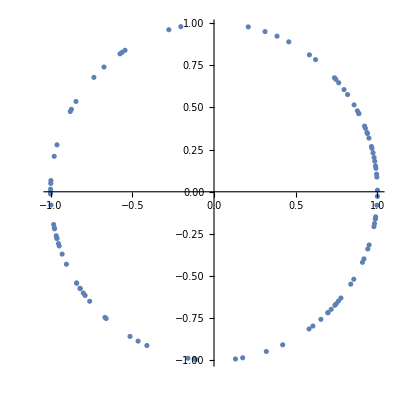

```mathematica
ListPlot[{Cos[#],Sin[#]}&/@ϕ,AspectRatio->1]
```

```mathematica
Table[If[Abs[i-j]==1,Abs[ϕ[[i]]-ϕ[[j]]],10],{i,Length[ϕ]},{j,Length[ϕ]}]
```

```mathematica
ℛ=ImplicitRegion[x^2+(y-1)^2≤1&&0<y<η,{x,y}];
Integrate[1,{x,y}∈ℛ,Assumptions->0<η<2]
```

Piecewise[{{√(2-η) η^(3/2)-√(-(-2+η) η)+ArcSin[√(-(-2+η) η)], η<1}, {π/2, η==1}, {√(2-η) η^(3/2)-√(-(-2+η) η)+2 ArcCos[√(-(-2+η) η)]+ArcSin[√(-(-2+η) η)], True}}]

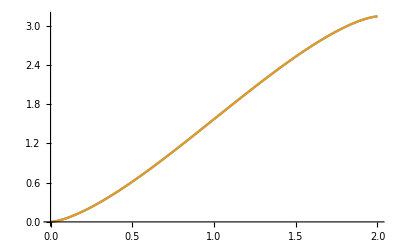

```mathematica
Plot[{%33,%37},{η,0,2}]
```

```mathematica
2Integrate[√(1-(1-y)^2),{y,0,η},Assumptions->0<η<2]//FullSimplify
π Integrate[1-(1-y)^2,{y,0,η},Assumptions->0<η<2]//FullSimplify
```

-√(-(-2+η) η)+√(-(-2+η) η^3)+2 ArcSin[(√η)/(√2)]

-1/3 π (-3+η) η^2